LevelScheme examples: Diagrams

M. A. Caprio, Department of Physics, University of Notre Dame

## Package initialization

If you have not already loaded the LevelScheme package since starting this Mathematica session, you must do so now.  See the user guide for information first on installing the package and then on loading it at the beginning of each Mathematica session.

```mathematica
Get["LevelScheme`"];
```

LevelScheme scientific figure preparation system
M. A. Caprio, Department of Physics, University of Notre Dame
Comput. Phys. Commun. 171, 107 (2005)
Version 3.52 (September 20, 2011)
View color paletteVisit home page  -Graphics-

## Diagram with various special arrow types

Note the uses of "squiggle" and "multiline" arrows

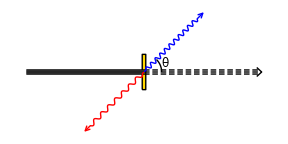

```mathematica
Figure[
{

(* target *)
SchemeSquare[{0,0},{0.03,0.3},FillColor->Gold],

(* beam *)
SetOptions[SchemeArrow,ArrowType->MultilineArrow,ShaftLines->3,FillColor->Gray],
SchemeArrow[{-2,0},{0,0},ShowHead->False,HeadLength->0],
SchemeArrow[{0,0},{2,0},Dashing->Automatic,ShowFill->False],

(* gamma rays *)
SetOptions[SchemeArrow,ArrowType->SquiggleArrow],
SchemeArrow[{0,0},{1,1},Color->Blue,SquiggleWavelength->8],
SchemeArrow[{0,0},{-1,-1},Color->Red,SquiggleWavelength->12],
SchemeCircle[{0,0},0.3,{0,Pi/4},ShowFill->False,LabR->"θ",NudgeR->10]

},
PlotRange->{{-2,2},{-1,1}},
ImageSize->72*{4,2}
]
```

## SU(2) laddering

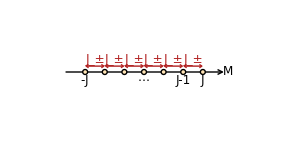

```mathematica
Figure[
{

SchemeLine[{{-4,0},{4,0}},ShowHead->True,LabR->textit["M"]],
lab[-3]=Row[{"-",textit["J"]}],
lab[-2]=None,
lab[-1]=None,
lab[0]="⋯",
lab[+1]=None,
lab[+2]=Row[{textit["J"],"-1"}],
lab[+3]=Row[{textit["J"]}],
Table[
SchemeCircle[{M,0},Point[3],FillColor->Moccasin,
LabB->lab[M]],
{M,-3,3}
],
Table[
SchemeLine[{{M-1+0.05,0.1},{M-0.05,0.1}},ShowTail->True,ShowHead->True,Color->Firebrick,HeadLip->2,HeadLength->3,LabT->Subscript[textit["J"],"±"],OffsetT->{0,-1},PosnT->0.5,BufferT->0],
{M,-2,3}
],
},
PlotRange->{{-6,6},{-1,1}},
ImageSize->72*{4,2}
]
```

## Dipole-dipole interaction: Ellipses and arrows

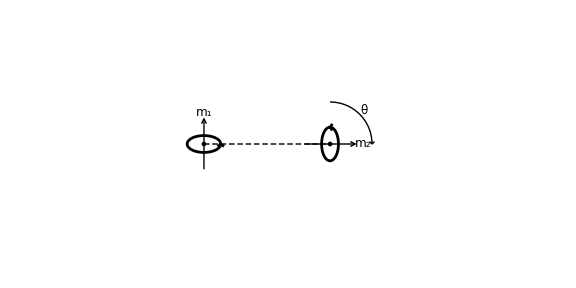

```mathematica
Figure[
{

SetOptions[SchemeArrow,Thickness->1,PosnC->1],
SetOptions[SchemeEllipse,ShowFill->False,ShowHead->True,HeadLength->3,HeadLip->4,Thickness->2],
sa=0.3,
rs=0.1,
rl=0.2,
P1={0,0},
P2={1.5,0},

SchemeCircle[P1,Point[2]],
SchemeArrow[P1+Polar@{sa,-Pi/2},P1+Polar@{sa,+Pi/2},
LabC->SubscriptBox[textbf["m"],"1"],OffsetC->{0,-1},OrientationC->Horizontal
],
SchemeEllipse[P1,{rl,rs},0],

SchemeCircle[P2,Point[2]],
SchemeArrow[P2+Polar@{sa,Pi},P2+Polar@{sa,0},
LabC->SubscriptBox[textbf["m"],"2"],OffsetC->{-1.5,0},OrientationC->Horizontal
],
SchemeEllipse[P2,{rl,rs},Pi/2],
SchemeCircle[P2,0.5,{0,Pi/2},ShowTail->True,LabX->"θ",ShowFill->False,HeadLength->3],
SchemeLine[{P1,P2},Dashing->True]

},
PlotRange->{{-1,3},{-1,1}},
ExtendRange->0.2,
ImageSize->72*{8,4}
]
```

## Internal reflection

```mathematica
LineEndpoints[theta_,d_,{L1_,L2_}]:={
d*{Cos[theta],Sin[theta]}+L1*{-Sin[theta],Cos[theta]},
d*{Cos[theta],Sin[theta]}+L2*{-Sin[theta],Cos[theta]}
};
```

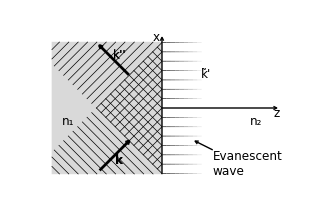

```mathematica
Figure[
{

zm=2.5,
zme=0.4*zm,
xm=1.5,
head=0.1,
lambda=0.15,
side=xm*Cos[theta],
infinity=999,
theta=45*Degree,
nj=10,

SetOptions[SchemeArrow,HeadLength->4,HeadLip->2],
SetOptions[SchemeAxis,HeadLength->4,HeadLip->2],

(* axes *)
SchemeAxis[Bottom,{0,zm+head},0,LabB->textit["z"],PosnB->1],
SchemeAxis[Left,0,{-xm,xm+head},LabL->textit["x"],PosnL->1,OrientationL->Horizontal],
SchemeBox[{{-zm,0},{-xm,xm}},FillColor->LightGray,ShowLine->False,Layer->-1],

SetOptions[SchemeArrow,BackgroundL->LightGray,BufferL->1.3,Thickness->2],
SetOptions[SchemeLine,Thickness->0.5],

(* plane waves *)
(* clip wavefronts to region with SetRegion *)
SetRegion[{{-zm,0},{-xm,xm}},{{-zm,0},{-xm,xm}}],
Table[
SchemeLine[LineEndpoints[theta,lambda*i,{side,-infinity}]],
{i,-20,20}
],
Table[
SchemeLine[LineEndpoints[-theta,lambda*i,{-side,infinity}]],
{i,-20,20}
],
SetRegion[],
SchemeArrow[{Polar[{-2,theta}],Polar[{-side,theta}]},LabL->textbf["k"]],
SchemeArrow[Reverse@{Polar[{-2,-theta}],Polar[{-side,-theta}]},LabL->SuperPrime[textbf["k"],2]],

(* evanescent wave *)
SetRegion[{{0,zm},{-xm,xm}},{{0,zm},{-xm,xm}}],
Table[
SchemeLine[{{zme/nj*(j-1),lambda/Sin[theta]*i},{zme/nj*j,lambda/Sin[theta]*i}},
LineColor->GrayLevel[j/nj],
Show->(i!=0)
],
{i,-8,8},{j,1,nj}
],
SetRegion[],
ManualLabel[{zme,0.5*xm},SuperPrime[OverTilde[textbf["k"]]]],

ManualLabel[{-0.85*zm,-0.2*xm},Subscript[textit["n"],"1"]],
ManualLabel[{+0.85*zm,-0.2*xm},Subscript[textit["n"],"2"]],

SetOptions[SchemeArrow,Thickness->1],
SchemeArrow[{{0.3*zm,-0.5*xm}+{0.4,-0.2},{0.3*zm,-0.5*xm}},
LabT->StackText[Center,0,{"Evanescent","wave"}],OrientationT->Horizontal,OffsetT->{-1.1,+1}]

},
PlotRange->{{-3,3},{-2,2}},
ImageSize->72*0.75*{6,4}
]
```

## Rotating inhomogeneous sphere

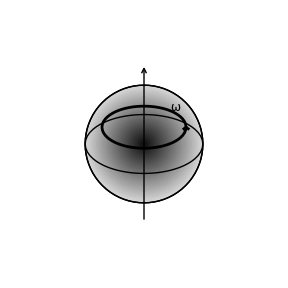

```mathematica
Figure[
{

SetOptions[SchemeArrow,Thickness->1,PosnC->1],
SetOptions[SchemeCircle,FillColor->Gray],
SetOptions[SchemeEllipse,ShowFill->False],

(* set various radius parameters *)
ra=0.5,
hb=0.2,
rb=0.7,
rc=0.9,

a=0,
b=rb,
dr=0.01,
lmin=0.05,
lmax=0.85,

(* make cloud-like gradient fill out of successively darker (as we move inward) concentric circles *)
Table[
SchemeCircle[{0,0},Horizontal[r],FillColor->GrayLevel[lmin+(lmax-lmin)/(b-a)*(r-a)],ShowLine->False],
{r,b,a+dr,-dr}
],
SchemeCircle[{0,0},rb,ShowFill->False],

(* annotations *)
SchemeCircle[{0,0},Horizontal[rb],ShowFill->False],
SchemeArrow[Polar[{rc,-Pi/2}],Polar[{rc,+Pi/2}]],
SchemeEllipse[{0,hb},Horizontal[{ra,0.5*ra}],ShowHead->True,HeadLength->3,HeadLip->4,Thickness->2,
LabX->"ω",PosnX->Pi],
SchemeEllipse[{0,0},Horizontal[{rb,0.5*rb}],0,{Pi,2*Pi}],
SchemeEllipse[{0,0},Horizontal[{rb,0.5*rb}],0,{0,Pi},Dashing->3],

},
PlotRange->{{-1,1},{-1,1}},
ExtendRange->0.2,
ImageSize->72*{4,4}
]
```

## Some more (circles, arrows, arcs, etc.)

Note how functions (Dipole and ForceArrow) have been defined to draw parts of the diagram, thereby saving retyping and allowing easy changes to the coordinates.  For instance, the "dipole" can be moved or its size changed just by changing the argument to Dipole, without the need to manually edit the coordinates for each component of the dipole.

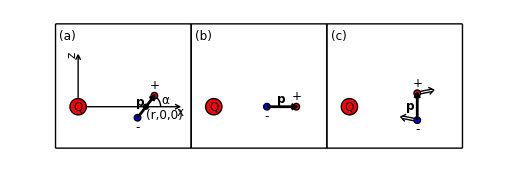

```mathematica
Dipole[x0_List,a_,theta_]:=Module[
{avec},
{
avec=a*{Cos[theta],Sin[theta]};
SchemeCircle[x0+avec,Point[4],FillColor->Red,LabT->"+"],
SchemeCircle[x0-avec,Point[4],FillColor->Blue,LabB->"-"],
SchemeArrow[{x0-avec,x0+avec},LabR->textbf["p"],Thickness->2,BufferR->1.3,OrientationR->If[N[theta]<Pi/2,Automatic,Inverted]]
}
];
ForceArrow[x_List,l_]:=Module[
{rhat},
rhat=x/Norm[x];
SchemeArrow[{x,x+l*rhat},ArrowType->MultilineArrow,ShowFill->False,Layer->0,Width->3]

];
Figure[
{
Multipanel[
{{0,1},{0,1}},
{1,3},
Margin->10,
XPlotRanges->{-0.2,1},
YPlotRanges->{-0.4,0.8},
XFrameTicks->None,YFrameTicks->None
],

x0={0.6,0},
a=0.13,
l=0.15,

FigurePanel[{1,1}],

SchemeAxis[Bottom,{0,0.9},0,LabB->textit["x"],PosnB->1],
SchemeAxis[Left,0,{0,0.5},LabL->textit["z"],PosnL->1],

SchemeCircle[{0,0},Point[10],FillColor->Red,LabC->textit["Q"]],
Dipole[x0,a,55*Degree],
SchemeCircle[x0,a,{0,45*Degree},ShowFill->False,LabX->"α",PosnX->0.3,Layer->0],
SchemeCircle[x0,Point[3],LabB->Row[{"(",textit["r"],",0,0)"}],OffsetB->{-1,+1}],

FigurePanel[{1,2}],

SchemeCircle[{0,0},Point[10],FillColor->Red,LabC->textit["Q"]],
Dipole[x0,a,0*Degree],

FigurePanel[{1,3}],

SchemeCircle[{0,0},Point[10],FillColor->Red,LabC->textit["Q"]],
Dipole[x0,a,90*Degree],
ForceArrow[x0+{0,a},l],
ForceArrow[x0+{0,-a},-l]

},
PlotRange->{{0,1},{0,1}},
ImageSize->72*0.8*{9,3}
]
```

## Diagram of recurrence relations

Figure from F. Q. Luo and M. A. Caprio, Nuclear Physics A 849, 35 (2011).

This provides an example of defining functions to draw certain elements of the figure which you use repeatedly within the figure (e.g., nodes of a network) and then of using "Table[]" to construct the full figure.

This also provides an example of maintaining multiple variants of a figure in parallel using "conditional inclusion", so that any changes you make automatically apply to both/all versions.  Two variants are needed here: 
	1) With SchemeFlags → {"EqnNumber"}, we make a version for use in the paper, with cross references to certain equation numbers.
	2) With SchemeFlags → {"Color"}, we make a color version for use in presentations.

Character definition
Incidentally, this figure also provides a simple example of selecting a different font to get a symbol we need.  In Times Roman, a lowercase italic "v" looks very similar to a lowercase Greek "ν".  We are trying to avoid this by using a different font for "v", namely, "BookAntiqua".  If you do not have "BookAntiqua" installed as a font on your system, you may not get this rounded v character in the example, or you may have to hunt for another suitable font if you really want it!  (For instance, "BookmanOldStyle" works well.)

```mathematica
RoundedV=Style["v",Italic,FontFamily->"BookAntiqua"]
```

v

Diagram components: Nodes

```mathematica
OverlapDot[v_,N_]:={
SchemeCircle[{N,v},DotRadius,ShowLine->False],
SchemeCircle[{N,v},DotScale*DotRadius,ShowFill->False,Show->(v==0)],
};
OBMEDot[v_,N_]:=SchemeCircle[{N,v+0.5},DotRadius,ShowLine->False];
UpEllipsis[v_,N_]:=ManualLabel[{N,v+0.5+0.25},"⋮"];
```

Diagram components: Arrows

```mathematica
OverlapNetwork[v_,N_]:={
SchemeArrow[{{N,v}+LL,{N,v-0.5}+UL}],
SchemeArrow[{{N,v}+LR,{N,v-1}+UR}]
};
OBMENetwork[v_,N_]:={
SchemeArrow[{{N,v+0.5}+ML,{N-1,v+0.5}+MR},Show->(N>0)],
SchemeArrow[{{N,v+0.5}+LL,{N-1,v}+UR},Show->(N>0)],
SchemeArrow[{{N,v+0.5}+LC,{N,v}+UC},Show->(v>0)]
};
```

Diagram components: Labels

```mathematica
OverlapLabel[v_]:=ManualLabel[{-0.5,v},Subsuperscript[textit["O"],textit["N"],Row[{"(",v,")"}]]];
OBMELabel[v_]:=ManualLabel[{-0.5,v+0.5},Subsuperscript[textit["T"],textit["N"],Row[{"(",v,")"}]]];
OverlapRecur[v_]:=ManualLabel[{NMax+0.5,v-0.25},Row[{"(",OverlapEquations[[v+1]],")"}],Show->(v>0)];
OBMERecur[v_]:=ManualLabel[{NMax+0.5,v+0.5-0.25},Row[{"(",OBMEEquations[[v+1]],")"}]];
OverlapEquations={None}~Join~Range[54,54+3];
OBMEEquations=Range[47,47+4];
```

Draw figure

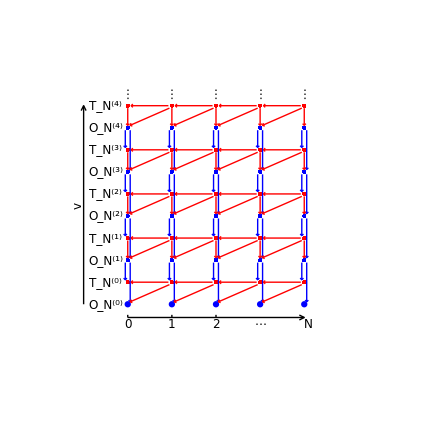

```mathematica
Figure[
{

SetOptions[SchemeArrow,HeadLip->2,HeadLength->2],

(* define network size *)
vMax=4;
NMax=4;

(* define dot dimensions *)
DotRadius=ConvertCoordinate[AbsoluteCoords,{2,2},D];
DotScale=1.5;

UR=DotScale*DotRadius*{1,1};
UC=DotScale*DotRadius*{0,1};
UL=DotScale*DotRadius*{-1,1};

ML=Sqrt[2]*DotScale*DotRadius*{-1,0};
MR=Sqrt[2]*DotScale*DotRadius*{+1,0};

LR=DotScale*DotRadius*{1,-1};
LC=DotScale*DotRadius*{0,-1};
LL=DotScale*DotRadius*{-1,-1};

(* axes *)
SchemeAxis[Left,-1,{0,vMax+0.5},LabL->RoundedV],
SchemeAxis[Bottom,{0,NMax},-0.3,LabB->textit["N"],Ticks->{{0,"0"},{1,"1"},{2,"2"},{3,"⋯",{0,0}}},PosnB->1,OffsetB->{-1,1},BufferB->0],

(* side labels *)
Table[
{OverlapLabel[v],OBMELabel[v]},
{v,0,vMax}
],
SchemeIfDef[
"EqnNumber",
Table[
{OverlapRecur[v],OBMERecur[v]},
{v,0,vMax}
]
],

(* top labels *)
Table[
UpEllipsis[vMax,N],
{N,0,NMax}
],

(* DEBUGGING: on network arrows, use dummy index names different from (N,v), to prevent bizarre errors when function definition dummy index has same name as loop dummy index *)

(* nodes and arrows*)
BlockSchemeOptions[
{
SetOptions[SchemeObject,Color->SchemeIfElseDef["Color",Blue,Black]],
Table[OverlapDot[v,N],{N,0,NMax},{v,0,vMax}],
Table[OverlapNetwork[vx,Nx],{Nx,0,NMax},{vx,1,vMax}]
}
],
BlockSchemeOptions[
{
SetOptions[SchemeObject,Color->SchemeIfElseDef["Color",Red,Gray]],
Table[OBMEDot[v,N],{N,0,NMax},{v,0,vMax}],
Table[OBMENetwork[vx,Nx],{Nx,0,NMax},{vx,0,vMax}]
}
],

},
PlotRange->{{-2,6},{-2,6}},
ImageSize->72*{6,6},
SchemeFlags->{"Color"}
]
(* clear some variable names used in example below *)
Clear[DotScale,DotRadius]
```

For the paper, we instead use
	SchemeFlags → {"EqnNumber"}

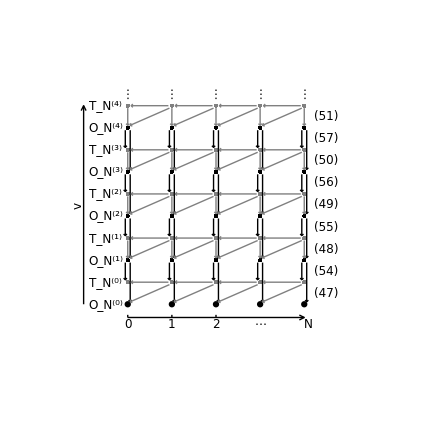

## Nuclear structure: A multipanel diagram

This provides plenty of examples of defining functions to draw different diagram elements, and also an example of PDF import.

import PDF graphics

```mathematica
EllipsoidGraphics=Import["LevelScheme/ExampleData/nuclpict_modes_redblue_Y22C.pdf"];
```

generate points for plot

```mathematica
ParamFcn[eta0_,xi_,x0_,x_]:=eta0*(1-Tanh[(x-x0)/xi]);
ParamPlot=Plot[ParamFcn[0.5,2,3,x],{x,0,5},PlotRange->{0,1}];
BCSPoints=Reverse/@GrabPoints[ParamPlot];
```

define simple (or maybe not-so-simple) functions to draw particles in pairing diagram

```mathematica
Options[ShellPoint]={N->6};
ShellPoint[y_Integer,(k_?NumericQ)?Positive,OptionsPattern[]]:={k/(OptionValue[N]+1),y};
```

```mathematica
Options[ShellDot]={DotRadius->Point[2],DotOptions->{},Occupied->True};
ShellDot[y_Integer,(k_?NumericQ)?Positive,OptionsPattern[]]:=Module[
{},
{
SchemeCircle[ShellPoint[y,k],OptionValue[DotRadius],OptionValue[DotOptions],ShowFill->OptionValue[Occupied]]
}
];
```

```mathematica
Options[ShellPair]={ExtraRadius->{0,0},NucleonShift->0,PairOptions->{},NucleonOptions->{},ArrowOptions->{},ArrowVector->{0,0.2}};
ShellPair[y_Integer,(k_?NumericQ)?Positive,OptionsPattern[]]:=Module[
{
P1,P2
},
{
P1=ShellPoint[y,k+OptionValue[NucleonShift]];
P2=ShellPoint[y,k+1-OptionValue[NucleonShift]];

SchemeCircle[
Mean[{P1,P2}],
1/2*(P2-P1)+OptionValue[ExtraRadius],
OptionValue[PairOptions]
],
ShellDot[y,k+OptionValue[NucleonShift],OptionValue[NucleonOptions]],
ShellDot[y,k+1-OptionValue[NucleonShift],OptionValue[NucleonOptions]],
SchemeArrow[{P1-OptionValue[ArrowVector],P1+OptionValue[ArrowVector]},OptionValue[ArrowOptions]],
SchemeArrow[{P2+OptionValue[ArrowVector],P2-OptionValue[ArrowVector]},OptionValue[ArrowOptions]]
}
]
```

define functions to draw particles in a circle for shell model schematic

```mathematica
DrawParticle[R_,theta_,r_,Opts___?OptionQ]:=SchemeCircle[ConvertCoordinate[AbsoluteCoords,UserCoords,D,R*{Cos[theta],Sin[theta]}],Point[r],Opts];
NaturalDistance[dtheta_,r_]:=r*Sec[1/2*(Pi-dtheta)];
```

put it all together

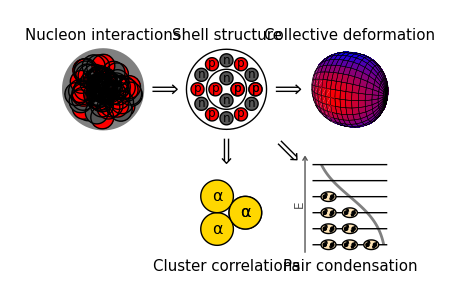

```mathematica
Figure[
{

Multipanel[
{{0,1},{0,1}},
{2,3},
XPlotRanges->{-1,1},
YPlotRanges->{-1,1},
ExtendRange->0.25,
Frame->False,
ShowPanelLetter->False
],

SetOptions[ScaledLabel,FontSize->15],


(* nucleus *)
FigurePanel[{1,1},PanelLetter->None],
ScaledLabel[{0.5,1},"Nucleon interactions",Offset->{0,+1}],
BlockSchemeOptions[
{
SeedRandom[3];
RNucl=1;
SchemeCircle[{0,0},RNucl,FillColor->Gray,ShowLine->False],
Table[
SchemeCircle[Polar[{0.7*RNucl*Random[],2*Pi*Random[]}],Point[14],FillColor->If[Random[Integer]==1,Red,DimGray]],
{n,1,100}
]
}
],

(* shell structure *)
FigurePanel[{1,2},PanelLetter->"(a)"],
ScaledLabel[{0.5,1},"Shell structure",Offset->{0,+1}],
BlockSchemeOptions[
{
RN=8,
R1=1.2*Sqrt[2]*RN,
R2=1.7*2.61*RN,
SetOptions[SchemeCircle,FillColor->Automatic,LabC->None],
TableForEach[
DrawParticle[R1,theta,RN,If[OddQ[i],{FillColor->Red,LabC->textit@"p",NudgeC->1},{FillColor->DimGray,LabC->textit@"n"}]],
{theta,i,Range[0,2*Pi,2*Pi/4]}
],
TableForEach[
DrawParticle[R2,theta,RN,If[OddQ[i],{FillColor->Red,LabC->textit@"p",NudgeC->1},{FillColor->DimGray,LabC->textit@"n"}]],
{theta,i,Range[0,2*Pi,2*Pi/12]}
],
SetOptions[SchemeCircle,ShowFill->False],
SchemeCircle[{0,0},Point[(R1+R2)/2]],
SchemeCircle[{0,0},Point[2*(R1+R2)/2]]
}
],

(* deformation *)
FigurePanel[{1,3},ExtendRange->0.15,PanelLetter->"(b)"],
ScaledLabel[{0.5,1},"Collective deformation",Offset->{0,+1}],
FigGraphics[{{-1,1},{-1,1}},EllipsoidGraphics],

(* alpha cluster *)
FigurePanel[{2,2},PanelLetter->"(c)"],
ScaledLabel[{0.5,0},"Cluster correlations",Offset->{0,-1}],
BlockSchemeOptions[
{
Ralpha=20,
SetOptions[SchemeCircle,FillColor->Gold,LabC->"α",FontSize->16],
Table[
DrawParticle[2/Sqrt[3]*Ralpha,theta,Ralpha],
{theta,0,2*Pi,2*Pi/3}
]
}
],

(* pairing *)
FigurePanel[{2,3},PlotRange->{{-0.25,1.25},{-1.5,5.5}},ExtendRange->0.05,PanelLetter->"(d)"],
ScaledLabel[{0.5,0},"Pair condensation",Offset->{0,-1}],
BlockSchemeOptions[
{
SetOptions[SchemeAxis,HeadLength->5,HeadLip->3,Color->DimGray],
SchemeAxis[Left,-0.1,{-0.5,5.5},LabL->textit["E"]],
SetOptions[Lev,Margin->0],
SetOptions[ShellPair,NucleonShift->0.15,ExtraRadius->{0.05,0.3},PairOptions->{FillColor->Moccasin},
ArrowOptions->{HeadLength->2,HeadLip->2},ArrowVector->{0.025,0.2}],
Table[
Lev[0,1,i],
{i,0,5}
],
ShellPair[0,1],
ShellPair[0,3],
ShellPair[0,5],
ShellPair[1,1],
ShellPair[1,3],
ShellPair[2,1],
ShellPair[2,3],
ShellPair[3,1],
(*Table[ShellDot[0,k],{k,1,6}],*)

SchemeLine[BCSPoints,Thickness->2,Color->Gray,Layer->0]
}
],

(* interpanel arrows *)
Px=0.1,
Do[
FigurePanel[{i,j}];
SavePoint[PL[i,j],{Px,0.5},ScaledCoords];
SavePoint[PR[i,j],{1-Px,0.5},ScaledCoords];
SavePoint[PT[i,j],{0.5,1-Px},ScaledCoords];
SavePoint[PB[i,j],{0.5,Px},ScaledCoords];
SavePoint[PTL[i,j],{Px/Sqrt[2],1-Px/Sqrt[2]},ScaledCoords];
SavePoint[PBR[i,j],{1-Px/Sqrt[2],Px/Sqrt[2]},ScaledCoords],
{i,1,2},{j,1,3}
];
SetRegion[],
SetOptions[SchemeArrow,ArrowType->MultilineArrow,ShowFill->False],
SchemeArrow[GetPoint[PR[1,1]],GetPoint[PL[1,2]]],
SchemeArrow[GetPoint[PR[1,2]],GetPoint[PL[1,3]]],
SchemeArrow[GetPoint[PB[1,2]],GetPoint[PT[2,2]]],
SchemeArrow[GetPoint[PBR[1,2]],GetPoint[PTL[2,3]]],



},
PlotRange->{{0,1},{0,1}},
ImageSize->72*0.7*{9,6},
Frame->False
]
```

## Simple example of image or vector graphics import

Import bitmap image from standard Wolfram example data (this is a Mathematica Image object)

```mathematica
MapImage=Import["ExampleData/cea.tif"];
```

Import vector graphics from a PDF file (this is a Mathematica Graphics object)

```mathematica
EllipsoidGraphics=Import["LevelScheme/ExampleData/nuclpict_modes_redblue_Y22C.pdf"];
```

```mathematica
Figure[
{
Multipanel[
{{0,1},{0,1}},
{2,2},
XPlotRanges->{0,1},
YPlotRanges->{0,1},
Frame->True,
XGapSizes->0.05,
YGapSizes->0.05,
ShowTicks->{False,False,False,False}
],

Table[

Switch[Mod[r+s,2],
0,
{
FigurePanel[{r,s},PanelLetterBackground->LightGray],
FigGraphics[{{0,1},{0,1}},MapImage],
},
1,
{
FigurePanel[{r,s},ExtendRange->0.05,Background->Moccasin],
FigGraphics[{{0,1},{0,1}},EllipsoidGraphics],
}
],
{r,1,2},{s,1,2}
]

},
PlotRange->{{0,1},{0,1}},
ExtendRange->0.1,
ImageSize->72*{4,4},
Frame->False
]
```

-Graphics-